# CCBH and Power Law + Peak: Formation mass distribution for m2

Davi  C. Rodrigues (this code).  2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled Black Hole (arbitrary k value)
DEBH = Dark Energy coupled Black Hole (implies k = - 3w)
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Directories.wl";

(*
  Calling wl files
  ***************** 
*)
getCode["Constants.wl"];
baseSimPoints = 10^7; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

getCode["ObsDataPreparationGWTC-3.wl"]; (*Not essential for this notebook*)
getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];
getCode["MassFactorCorrection.wl"];

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

findSigma::usage = "findSigma[probability] yields the number of σ's for a given probability.";
findSigma[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[outSigma];
outSigma[n_] := outSigma[n] = NProbability[Abs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting ObsDataPreparationGWTC-3.wl:

Number of m1 black holes:   72

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

Starting MassFactorCorrection.wl:

Base number of simmulated points per dimension (baseSimPoints):   10000000

"dataM1Merger"  57.8192

End of running wl files.

```mathematica
Off[NIntegrate::slwcon];
(*plpp`listPiM2; *)(*Takes about 15 minutes. For sure this can be faster, but it works. Parallelizing is not very helpful*)
(*dumpsave["plpplistPiM2.mx", plpp`listPiM2]*)
getAux["plpplistPiM2.mx"];
plpp`listPiM2
```

{{1.,0.},{1.5,0.},{2.,0.},{2.5,0.},{3.,0.},{3.5,0.},{4.,0.},{4.5,0.},{5.,4.58453×10^-12},{5.5,0.00622168},{6.,0.082013},{6.5,0.177178},{7.,0.222994},{7.5,0.226963},{8.,0.208283},{8.5,0.181361},{9.,0.147742},{9.5,0.1139},{10.,0.0874175},{10.5,0.0686766},{11.,0.0536483},{11.5,0.0438919},{12.,0.0364842},{12.5,0.030738},{13.,0.0262077},{13.5,0.0225861},{14.,0.0196449},{14.5,0.0172379},{15.,0.0152524},{15.5,0.0136009},{16.,0.0122071},{16.5,0.0110331},{17.,0.0100399},{17.5,0.00918418},{18.,0.00845238},{18.5,0.00782308},{19.,0.00727742},{19.5,0.00680386},{20.,0.00639049},{20.5,0.0060305},{21.,0.00571562},{21.5,0.0054384},{22.,0.00519602},{22.5,0.00498263},{23.,0.00450617},{23.5,0.00462876},{24.,0.00448152},{24.5,0.00435285},{25.,0.00424},{25.5,0.00413875},{26.,0.00405047},{26.5,0.00397253},{27.,0.00390509},{27.5,0.00384622},{28.,0.00379364},{28.5,0.00374702},{29.,0.0037042},{29.5,0.00366332},{30.,0.00361948},{30.5,0.00356696},{31.,0.00349678},{31.5,0.00339784},{32.,0.00326306},{32.5,0.00307968},{33.,0.00284455},{33.5,0.00256732},{34.,0.00225277},{34.5,0.00192237},{35.,0.00159647},{35.5,0.00129684},{36.,0.00103772},{36.5,0.000828624},{37.,0.00066911},{37.5,0.000553451},{38.,0.000472927},{38.5,0.000417949},{39.,0.00037983},{39.5,0.000352618},{40.,0.00033145},{40.5,0.000313814},{41.,0.000298672},{41.5,0.000284888},{42.,0.000271712},{42.5,0.000259626},{43.,0.000248248},{43.5,0.000237227},{44.,0.000226957},{44.5,0.000217281},{45.,0.000207784},{45.5,0.000199053},{46.,0.000190572},{46.5,0.000182582},{47.,0.00017494},{47.5,0.000167626},{48.,0.000160662},{48.5,0.000154181},{49.,0.000147815},{49.5,0.000141745},{50.,0.000135934},{50.5,0.000130487},{51.,0.000125241},{51.5,0.000120167},{52.,0.000115356},{52.5,0.000110829},{53.,0.000106439},{53.5,0.000102181},{54.,0.0000980895},{54.5,0.0000942474},{55.,0.0000904289},{55.5,0.0000867886},{56.,0.0000833848},{56.5,0.0000800657},{57.,0.0000769042},{57.5,0.0000738015},{58.,0.0000708661},{58.5,0.000068049},{59.,0.0000653068},{59.5,0.0000626119},{60.,0.0000601261},{60.5,0.0000577376},{61.,0.0000552807},{61.5,0.0000530401},{62.,0.0000508102},{62.5,0.0000486891},{63.,0.0000466618},{63.5,0.0000446566},{64.,0.0000427533},{64.5,0.0000408987},{65.,0.0000391147},{65.5,0.000037377},{66.,0.0000357086},{66.5,0.0000342102},{67.,0.0000325043},{67.5,0.0000309689},{68.,0.0000295098},{68.5,0.0000280603},{69.,0.0000267069},{69.5,0.0000253586},{70.,0.0000240318},{70.5,0.0000227638},{71.,0.0000215391},{71.5,0.0000203481},{72.,0.000019183},{72.5,0.0000180619},{73.,0.000016943},{73.5,0.0000158996},{74.,0.0000148592},{74.5,0.0000138472},{75.,0.0000128578},{75.5,0.0000119152},{76.,0.0000109739},{76.5,0.0000100773},{77.,9.19176×10^-6},{77.5,8.32139×10^-6},{78.,7.5023×10^-6},{78.5,6.68157×10^-6},{79.,5.88781×10^-6},{79.5,5.11408×10^-6},{80.,4.35387×10^-6},{80.5,3.61565×10^-6},{81.,2.8938×10^-6},{81.5,2.1934×10^-6},{82.,1.5032×10^-6},{82.5,8.32722×10^-7},{83.,1.80722×10^-7},{83.5,0.},{84.,0.},{84.5,0.},{85.,0.},{85.5,0.},{86.,0.},{86.5,0.},{87.,0.},{87.5,0.},{88.,0.},{88.5,0.},{89.,0.},{89.5,0.},{90.,0.},{90.5,0.},{91.,0.},{91.5,0.},{92.,0.},{92.5,0.},{93.,0.},{93.5,0.},{94.,0.},{94.5,0.},{95.,0.},{95.5,0.},{96.,0.},{96.5,0.},{97.,0.},{97.5,0.},{98.,0.},{98.5,0.},{99.,0.},{99.5,0.},{100.,0.}}

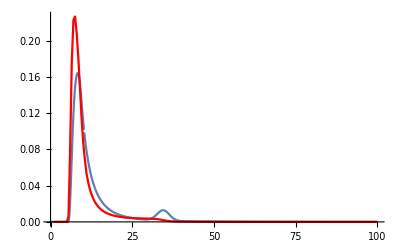

```mathematica
Show[Plot[plpp`pi[m1], {m1,0,100}, PlotPoints->40, PlotRange->All], ListPlot[plpp`listPiM2, Joined->True, PlotRange->All, PlotStyle->Red]]
```

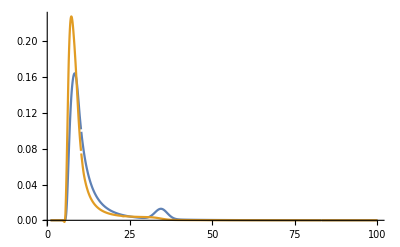

```mathematica
Plot[{plpp`pi[m1], plpp`piM2Inorm[m1]}, {m1,1,100}, PlotPoints->40, PlotRange->All]
```

```mathematica
#[RandomVariate[plpp`dist2[], 10^4]]  & /@  {Median, Mean} 
#[RandomVariate[plpp`dist[], 10^4]]  & /@  {Median, Mean}
```

{8.40554,10.278}

{10.3201,13.6402}

## Formation mass distribution

```mathematica
ClearAll[
  𝒟M1Formation, 
  𝒟M1FormationRaw
];

Clear[dataM2FormationRaw, dataM2Formation];
𝒟plp2 = plpp`𝒟2[]; 
dataM2Merger = RandomVariate[𝒟plp2, 2 baseSimPoints] ~ EchoTiming ~ "dataM2Merger"; 

dataM2FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_]:= dataM2FormationRaw[zObs, tdmin, tdmax, k, zMax, w]= Block[
  {length, dataM2MergerSameLength},
  length = Length @ dataMassFactor[zObs, tdmin, tdmax, k, zMax, w];
  dataM2MergerSameLength = Take[dataM2Merger, length];
  1/dataMassFactor[zObs, tdmin, tdmax, 1, zMax, w]^k dataM2MergerSameLength 
];

dataM2Formation[zObs_, opts:OptionsPattern[optionstkw]] := dataM2FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
]


𝒟M1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M1FormationRaw[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w],
  0.05, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {2,2}, (*This slightly extends the profile beyond data (about 0.1 solar mass). 
  It is only used for the plot. Use {0,0} for no extension.*)
  PerformanceGoal->"Quality"
];

𝒟M1Formation[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

𝒟M2FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M2FormationRaw[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataM2FormationRaw[zObs, tdmin, tdmax, k, zMax, w],
  0.05, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {2,2}, (*This slightly extends the profile beyond data (about 0.1 solar mass). 
  It is only used for the plot. Use {0,0} for no extension.*)
  PerformanceGoal->"Quality"
];

𝒟M2Formation[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M2FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

Clear[𝒟M2FormationEmpRaw, 𝒟M2FormationEmp]
𝒟M2FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M2FormationEmpRaw[zObs, tdmin, tdmax, k, zMax, w] = 
 EmpiricalDistribution[
   dataM2FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M2FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M2FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];
```

"dataM2Merger"  160.003

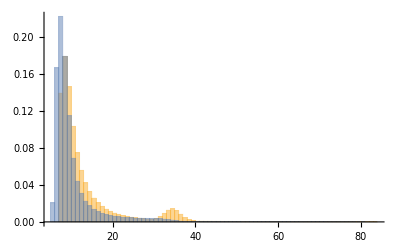

```mathematica
Histogram[{dataM1Merger, dataM2Merger}, {1}, "PDF", PlotRange->All]
```

## Main results:

```mathematica
probabilityMminApprox2[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M2FormationEmp[0.4, opts], mMin]^69; (*Assumes 69 m2 BH masses.*)
probabilityMminDoubleApprox2[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M2FormationEmp[0.4, opts], mMin]^(2*69);
```

```mathematica
{probabilityMminApprox2[2], findSigma@probabilityMminApprox2[2]}
```

{0.0000715994,3.97091}

```mathematica
0.00007159941350416846^(72/69) // findSigma
```

4.06868

```mathematica
{probabilityMminApprox2[2], findSigma@probabilityMminApprox2[2]}
```

4.03897

```mathematica
{probabilityMminDoubleApprox2[2], findSigma@probabilityMminDoubleApprox2[2]}
```

{5.12648×10^-9,5.84301}

```mathematica
tdmaxE = 5;
tdminE = 0.005;
zMaxE = 2;
𝒟M2Formation[0.4]; //EchoTiming
𝒟M2Formation[0.4, k-> 0.5]; //EchoTiming
𝒟M2Formation[0.4, tdmax -> tdmaxE]; //EchoTiming
𝒟M2Formation[0.4, tdmin -> tdminE]; //EchoTiming
𝒟M2Formation[0.4, zMax -> zMaxE]; //EchoTiming

legend1 = LineLegend[
  {Lighter@Orange, ColorData["AvocadoColors"][0.5], Lighter@Blue}, 
  {
    Style["k=3.0", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.5", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.0", FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 20, 
  Spacings -> 0.15 (*It works, although in red*)
];

legend2 = LineLegend[
  {Directive[Lighter@Orange, Dashed], Directive[Lighter@Orange, Dotted], Directive[Lighter@Orange, DotDashed]}, 
  {
    Style["t_max=" <> ToString[Round@tdmaxE]<>" Gyr", FontFamily->"Times", FontSize -> 11], 
    Style["t_min=" <> ToString[Round[10^3 tdminE]]<>" Myr", FontFamily->"Times", FontSize -> 11],
    Style["z_max=" <> ToString[Round[zMaxE]], FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 20, 
  Spacings -> 0.15 (*It works, although in red*)
];

tickLarge = 0.015;
tickSmall = 0.006;
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -4, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -4, 0, 1}];
frameTicksLargeDumb = Table[{10^i, "", tickLarge}, {i, -4, 0, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksDumb = Flatten[Join[{frameTicksSmall, frameTicksLargeDumb}],1];


Off[General::munfl]; 
plotPDFformationDist2 = LogLogPlot[
  {
    PDF[𝒟M2Formation[0.4], x], 
    PDF[𝒟M2Formation[0.4, tdmax -> tdmaxE], x], 
    PDF[𝒟M2Formation[0.4, tdmin -> tdminE], x], 
    PDF[𝒟M2Formation[0.4, zMax -> zMaxE], x],
    PDF[𝒟M2Formation[0.4, k-> 0.5], x], 
    PDF[𝒟plp2, x]
  }, 
  {x, 0.5, plpp`mMax /. optionsPlpp}, 
  PlotRange->{{0.5, 500}, {8 10^-5, .3}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, frameTicksDumb}, {Automatic, Automatic}},
  PlotPoints->5000,
  MaxRecursion->3,
  PlotStyle->{
    {Lighter@Orange}, 
    {Lighter@Orange, Dashed}, 
    {Lighter@Orange, Dotted}, 
    {Lighter@Orange, DotDashed}, 
    {ColorData["AvocadoColors"][0.5]}, 
    {Lighter@Blue}},
  PlotLegends-> {Placed[legend1, {0.60,0.81}], Placed[legend2, {0.85,0.81}]}
]
On[General::munfl];

exportOut["plotPDFformationDist2.pdf", plotPDFformationDist2]
```

2.11645

117.271

87.1479

227.308

224.468

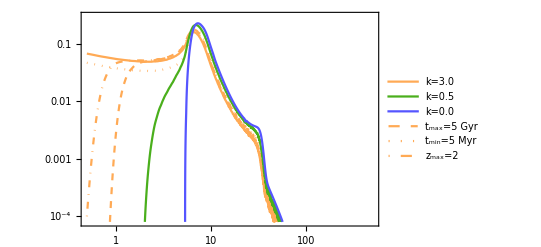

pathOut/plotPDFformationDist2.pdf